#### Case 2 (ν odd)

#### The problem

Our goal is to find a closed form expression for the integral

	(H^ν)_un(ϕ, b, r) = ∫_(π-ϕ)^(2π+ϕ) cos^u ψ sin^n ψ(1-r^2-b^2 - 2b r sin ψ)^(3/2)ⅆψ

for odd ν.

#### Rearranging

First, note that for b > 0 we can write

	(H^ν)_un(ϕ, b, r) = (2br)^(3/2)∫_(π-ϕ)^(2π+ϕ) cos^u ψ sin^n ψ(s - sin ψ)^(3/2)ⅆψ

where we define s = (1-r^2-b^2)/(2br) = 2 k^2-1, with k^2 defined in Appendix A1. 

Next, with some algebraic sleight of hand we can express the term in parentheses as

	(s - sin (ψ))^(3/2)= ⅈ(1 - s)^(3/2)Δ^3

where

	Δ = √(1-χ^2 sin^2 x)

with

	χ^2=2/(1- s)= 1/(1-k^2)

and

	x = π/4-ψ/2


We can check that the real parts of these expressions are equal. Let’s compute the maximum difference for given values of s between (say) -5 and 5:

```mathematica
Max[Abs[Table[
Re[(s-Sin[ψ])^(3/2)] -Re[ⅈ(1-s)^(3/2)(1-2/(1-s)Sin[π/4-ψ/2]^2)^(3/2)],
{ψ,π/2,2π+π/2,0.01},
{s,-5,5,0.0333}]]]
```

7.10543×10^-15

There are two caveats: 
	(1) our expression diverges when b = 0 (s = 1) 
	(2) the imaginary parts of the two expressions have different signs

We address the first point by noting that when b = 0, the term to the 3/2 power in the H integral factors out, so we’re back to Case 1 (ν even), which is easy to solve. The second point ends up not mattering, since the solution to the H integral *has* to be real (since it represents a real flux), so the imaginary parts will always cancel.

So let’s rewrite the integral as

	(H^ν)_un(ϕ, b, r) =ⅈ (2br)^(3/2)(1-s)^(3/2) ∫_(π-ϕ)^(2π+ϕ) cos^u ψ sin^n ψ (Δ(ψ))^3 ⅆψ

We can do the substitution ψ→x in the H integral:

	(H^ν)_un(ϕ, b, r) =2ⅈ (2br)^(3/2)(1-s)^(3/2) ∫_(-ϕ/2-(3π)/4)^(ϕ/2-π/4) cos^u(π/2-2x ) sin^n (π/2-2x ) (Δ(x))^3 ⅆx
   		          =2ⅈ (2br)^(3/2)(1-s)^(3/2) ∫_(-ϕ/2-(3π)/4)^(ϕ/2-π/4) sin^u(2x) cos^n (2x ) (Δ(x))^3 ⅆx
   		          =2ⅈ (2br)^(3/2)(1-s)^(3/2) ∫_(-ϕ/2-(3π)/4)^(ϕ/2-π/4) (2cos x sin x)^u (cos^2 x-sin^2 x)^n (Δ(x))^3 ⅆx
   		          =2^(u+1)ⅈ (2br)^(3/2)(1-s)^(3/2) ∫_(-ϕ/2-(3π)/4)^(ϕ/2-π/4) (cos x sin x)^u (cos^2 x-sin^2 x)^n (Δ(x))^3 ⅆx

We can use the binomial theorem to expand the (cos^2 x -sin^2 x)^n term:

	(H^ν)_un(ϕ, b, r) = 2^(u+1)ⅈ  (2br)^(3/2)(1-s)^(3/2)∑_(i=0)^n (-1)^(n-i)(n
i)∫_(-ϕ/2-(3π)/4)^(ϕ/2-π/4) cos^(u+2i)x sin^(u+2n-2i)x Δ^(3/2)ⅆx
And we can do some rearranging to write

	(H^ν)_un(ϕ, b, r)= 2^(u+3) (br)^(3/2)∑_(i=0)^n (-1)^(i-n-u)(n
i) J_(u+2i, u + 2n - 2i)

where

	J_pq = ⅈ (1-s)^(3/2)(-1)^q 1/(√2)∫_(-ϕ/2-(3π)/4)^(ϕ/2-π/4) cos^p x sin^q x Δ^(3/2)ⅆx
	      = 2(ⅈ(1-k^2))^(3/2)(-1)^q∫_(-ϕ/2-(3π)/4)^(ϕ/2-π/4) cos^p x sin^q x Δ^(3/2)ⅆx

#### The solution

The reason we rearranged into the form above is that integrals of the form

	∫ cos^p x sin^q x Δ^(3/2)ⅆx

are analytic and solvable via recursion relations (Gradshteyn & Ryzhik 5th edition p.192 #2.581). As we will see, in order for the recurrence to work, we need to have values for J_00,J_02,J_20,J_22. As it happens, odd q integrates to zero, while odd p integrates to something nonzero but is never actually needed in the recursion! So let’s only bother with J for even p and even q. Let’s start by defining some elliptic functions.

```mathematica
E1[k2_]:=If[k2<1,
(1-k2)EllipticK[k2],
(1-k2)/(√k2)EllipticK[1/k2]];

E2[k2_]:=If[k2<1,
EllipticE[k2],
√k2 EllipticE[1/k2]+(1-k2)/(√k2)EllipticK[1/k2]];
```

where k2 = k^2.

Now, from the equations in Gradshteyn & Ryzhik and with a lot of help from Mathematica, we can write our initial conditions:

```mathematica
J00[k2_]:=((8-12k2)/3)E1[k2]+((-8+16k2)/3)E2[k2];
J02[k2_]:=((8-24k2)/15)E1[k2]+((-8+28k2+12 k2^2)/15)E2[k2];
J20[k2_]:=((32-36k2)/15)E1[k2]+((-32+52k2-12 k2^2)/15)E2[k2];
J22[k2_]:=((32-60k2+12 k2^2)/105)E1[k2]+((-32+76k2-36 k2^2+24 k2^3)/105)E2[k2];
```

Note that I skipped some steps here. The solutions include sine and cosine terms, but these all cancel in the definite integrals!

We can easily check these expressions for k^2>0 by comparing to the *real part* of the direct numerical integration of the definition of Jpq:

```mathematica
ϕ[k2_]:=If[-1<2k2-1<1,ArcSin[2k2-1],π/2];
JNum[p_,q_,k2_]:= Re[NIntegrate[2ⅈ(1-k2)^(3/2)(-1)^q Cos[x]^p Sin[x]^q(1-1/(1-k2)Sin[x]^2)^(3/2),{x,-ϕ[k2]/2-(3π)/4,ϕ[k2]/2-π/4}]];
```

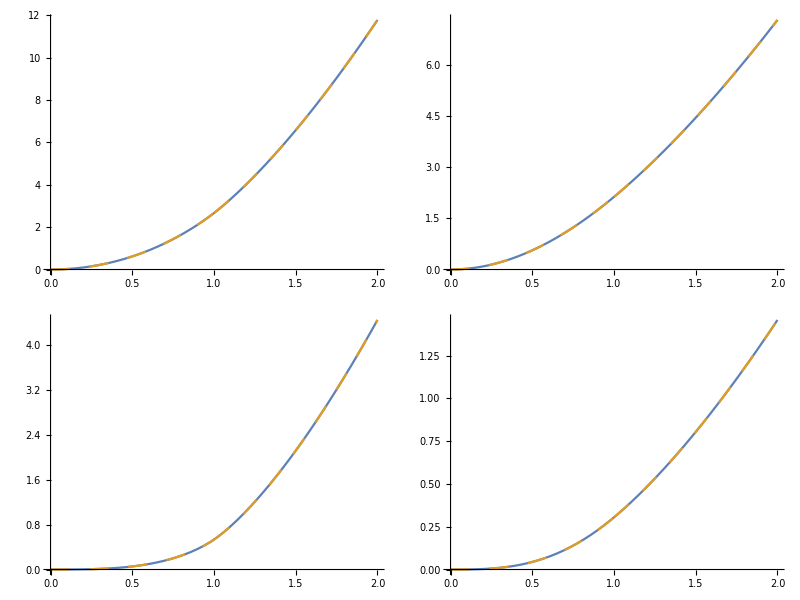

```mathematica
{{Plot[{JNum[0,0,With[{foo=k2},foo]],J00[k2]},{k2,0,2},PlotStyle->{Dashing[None],Dashing[Large]}],
Plot[{JNum[0,2,With[{foo=k2},foo]],J02[k2]},{k2,0,2},PlotStyle->{Dashing[None],Dashing[Large]}]},
{Plot[{JNum[2,0,With[{foo=k2},foo]],J20[k2]},{k2,0,2},PlotStyle->{Dashing[None],Dashing[Large]}],
Plot[{JNum[2,2,With[{foo=k2},foo]],J22[k2]},{k2,0,2},PlotStyle->{Dashing[None],Dashing[Large]}]}}//TableForm
```

Finally, we get to the recurrence relation, from Gradshteyn & Ryzhik:

```mathematica
J[p_,q_,k2_]:=Which[
OddQ[p],0,
OddQ[q],0,
(p==0 && q==0),J00[k2],
(p==0 && q==2),J02[k2],
(p==2 && q==0),J20[k2],
(p==2 && q==2),J22[k2],
True,Module[{d1,d2,d3,d4},
d1=q+2+(p+q-2)(1-k2);
d2=-(q-3)(1-k2);
d3=2p+q-(p+q-2)(1-k2);
d4=-(p-3)+(p-3)(1-k2);
Which[
q≥4,(d1 J[p,q-2,k2]+d2 J[p,q-4,k2])/(p+q+3),
p≥4,(d3 J[p-2,q,k2]+d4 J[p-4,q,k2])/(p+q+3),
True,None]
]
]
```

Let’s again compare this to the numerical solutions:

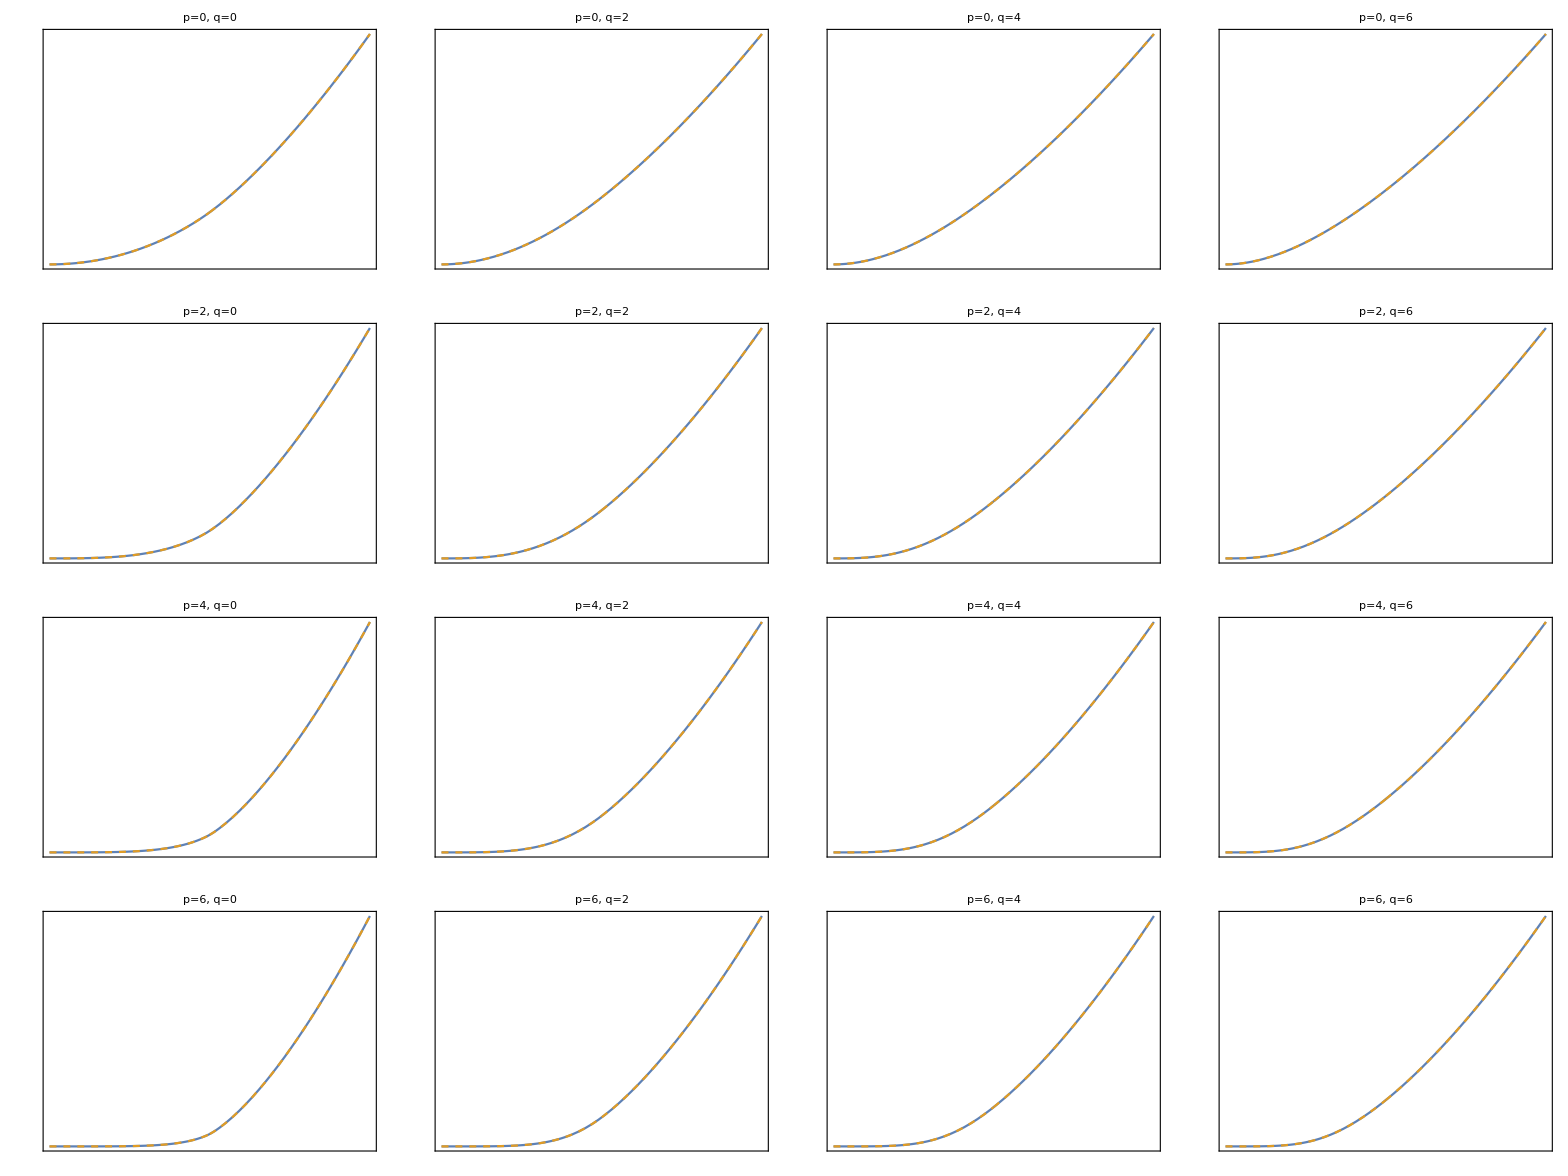

```mathematica
Table[
With[{r=0.5},Plot[{Evaluate[JNum[p,q,k2]],Evaluate[J[p,q,k2]]},{k2,0.,2.},PlotStyle->{Dashing[None],Dashing[Small]},Frame->True,Axes->False,AspectRatio->1,FrameTicks->None,PlotLabel->StringForm["p=``, q=``",p,q],ImageSize->Tiny]],{p,0,6,2},{q,0,6,2}
]//TableForm
```

#### Woot.